```mathematica
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@AbsoluteOptions[g,PlotRange],Sequence@@Options[g,Epilog]]
```

/home/zack/cantera/ratematrix

## Single runs

data/h2o2/8/

{48,23924,27.2978,2819670,25}

-Graphics- | -Graphics-

{17.4274,Null}

{17.3953,Null}

{17.3369,Null}

{17.3271,Null}

{17.3449,Null}

{0.242661,Null}

{0.244474,Null}

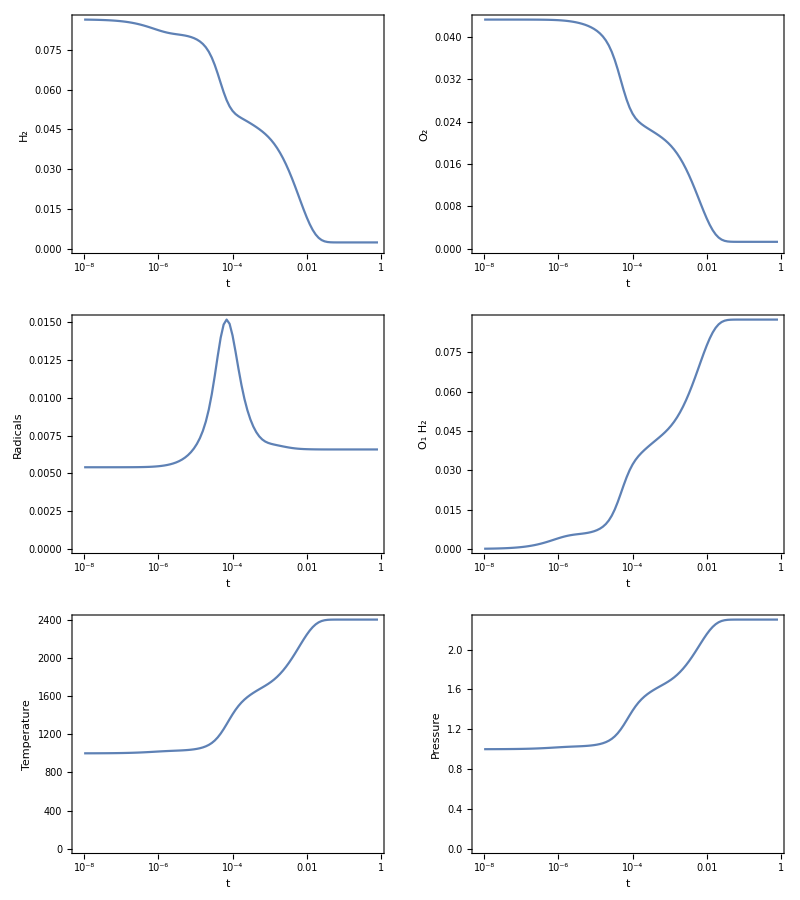

2399.63

2.30019

-9.41372×10^-6+0. ⅈ

```mathematica
filebase="data/h2o2/8/"
dat=Import[filebase<>"out.dat"];
{atoms, dim,runtime, count, level} = dat[[1,1;;5]]
elements=dat[[3]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Integer64"][[17;;-1]];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[spatoms]];
spforms=Table[DisplayForm[RowBox[Table[If[spatoms[[i,j]]>0,Subscript[elements[[j]],spatoms[[i,j]]],""],{j,1,Length[elements]}]]],{i,1,Length[spatoms]}];
multiforms=Table[Total[multiindices[[i]]*spforms],{i,1,dim}];
A=SparseArray[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}],{dim,dim}];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
Grid[{{rasterizeBackground[MatrixPlot[A,ImageSize->350,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,"Rate matrix"},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{105,25},{65,65}}]],rasterizeBackground[MatrixPlot[Table[Pi/2-ArcCos[Abs[evecs[[-i]].Conjugate[evecs[[-j]]]]/(Norm[evecs[[-i]]]*Norm[evecs[[-j]]])],{i,1,Length[evecs]},{j,1,Length[evecs]}],ImageSize->350,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,"Rate matrix"},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{105,25},{65,65}}]]}}]
states=Partition[BinaryReadList[filebase<>"propogate.npy","Real64"][[17;;-1]],dim];
times=BinaryReadList[filebase<>"times.npy","Real64"][[17;;-1]];
o2norm=DiagonalMatrix[((#[[4]])/Total[#])&/@multiindices];
h2norm=DiagonalMatrix[((#[[1]])/Total[#])&/@multiindices];
h2onorm=DiagonalMatrix[((#[[6]])/Total[#])&/@multiindices];
radicalnorm=DiagonalMatrix[((#[[2]]+#[[3]]+#[[5]]+#[[7]])/Total[#])&/@multiindices];
temperaturenorm=DiagonalMatrix[temperatures];
pressurenorm=DiagonalMatrix[pressures];
(*Abs[(Total[#]-Total[evecs[[-1]].h2norm]/Total[evecs[[-1]]])]*)
AbsoluteTiming[h2dats=Transpose[{times,Total[#]&/@(states.h2norm)}];]
AbsoluteTiming[o2dats=Transpose[{times,Total[#]&/@(states.o2norm)}];]
AbsoluteTiming[radicaldats=Transpose[{times,Total[#]&/@(states.radicalnorm)}];]
AbsoluteTiming[radicaldats=Transpose[{times,Total[#]&/@(states.radicalnorm)}];]
AbsoluteTiming[h2odats=Transpose[{times,Total[#]&/@(states.h2onorm)}];]
AbsoluteTiming[temperaturedats=Transpose[{times,Total[#]&/@(states.temperaturenorm)}];]
AbsoluteTiming[pressuredats=Transpose[{times,Total[#]&/@(states.pressurenorm)}];]
Grid[{{ListLogLinearPlot[h2dats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[1]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],ListLogLinearPlot[o2dats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[4]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350]},{ListLogLinearPlot[radicaldats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,HoldForm["Radicals" ]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],ListLogLinearPlot[h2odats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[6]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350]},{ListLogLinearPlot[temperaturedats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,"Temperature"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],ListLogLinearPlot[pressuredats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,"Pressure"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350]}}]
Re[Total[temperatures*evecs[[-1]]]/Total[evecs[[-1]]]]
Re[Total[pressures*evecs[[-1]]]/Total[evecs[[-1]]]]
1/evals[[1]]
```

```mathematica
Length[evals]
```

80

data/h2o2/6/

{36,6366,9.02314,496463,19}

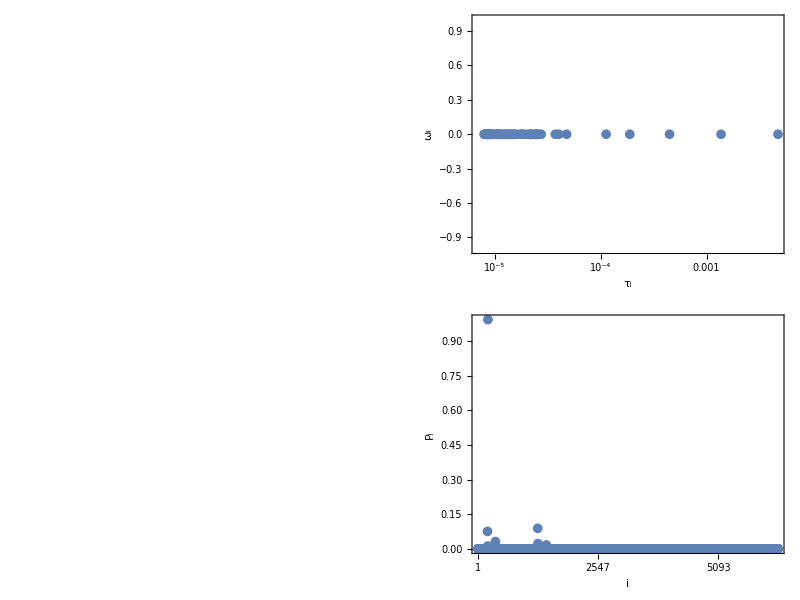

{120 (Ar_1)+O_1 H_1+12 (O_1 H_2),120 (Ar_1)+H_1+H_2+11 (O_1 H_2)+O_2,120 (Ar_1)+2 (H_2)+O_1 H_1+10 (O_1 H_2)+O_2,120 (Ar_1)+H_2+O_1+O_1 H_1+11 (O_1 H_2),120 (Ar_1)+H_1+2 (O_1 H_1)+11 (O_1 H_2)}

2409.76

2.30897

-7.97884×10^-6+0. ⅈ

```mathematica
filebase="data/h2o2/6/"
dat=Import[filebase<>"out.dat"];
{atoms, dim,runtime, count, level} = dat[[1,1;;5]]
elements=dat[[3]];
rows=BinaryReadList[filebase<>"rows.npy","Integer64"][[17;;-1]];
columns=BinaryReadList[filebase<>"columns.npy","Integer64"][[17;;-1]];
data=BinaryReadList[filebase<>"data.npy","Integer64"][[17;;-1]];
A=SparseArray[Table[{rows[[i]]+1,columns[[i]]+1}->data[[i]],{i,1,Length[data]}],{dim,dim}];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[spatoms]];
spforms=Table[DisplayForm[RowBox[Table[If[spatoms[[i,j]]>0,Subscript[elements[[j]],spatoms[[i,j]]],""],{j,1,Length[elements]}]]],{i,1,Length[spatoms]}];
multiforms=Table[Total[multiindices[[i]]*spforms],{i,1,dim}];
p=Grid[{{rasterizeBackground[MatrixPlot[A,ImageSize->350,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,"Rate matrix"},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{105,25},{65,65}}]],ListLogLinearPlot[{-1/Re[#],Im[#]}&/@evals[[1;;-2]],ImageSize->350,PlotRange->All,AspectRatio->1,Axes->False,Frame->True,FrameTicks->{{Automatic,None},{Automatic,None}},FrameLabel->{{DisplayForm[RowBox[{Subscript[ω,i]}]],None},{DisplayForm[RowBox[{Subscript[τ,i]}]],Subscript[λ,i]==1/Subscript[τ,i]+I*Subscript[ω,i]}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],PlotStyle->Directive[PointSize[0.02]],ImagePadding->{{105,25},{65,65}}]},{rasterizeBackground[MatrixPlot[Reverse[evecs],ImageSize->350,FrameTicks->{Table[Round[i],{i,1,dim,(dim-1)/5}],Table[Round[i],{i,1,dim,(dim-1)/5}]},FrameLabel->{{i,"Left eigenvectors"},{j,None}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImagePadding->{{105,25},{65,65}}]],ListPlot[Abs[evecs[[-1]]],ImageSize->350,PlotRange->All,Axes->False,Frame->True,FrameLabel->{{Subscript[P,i],None},{i,"Steady distribution"}},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1,FrameTicks->{{Automatic,None},{Table[Round[i],{i,1,dim,(dim-1)/5}],None}},PlotStyle->Directive[PointSize[0.02]],ImagePadding->{{105,25},{65,65}}]}}]
Total[spforms*#]&/@multiindices[[Reverse[Ordering[Abs[evecs[[-1]]]]][[1;;5]]]]
Re[Total[temperatures*evecs[[-1]]]/Total[evecs[[-1]]]]
Re[Total[pressures*evecs[[-1]]]/Total[evecs[[-1]]]]
1/evals[[1]]
```

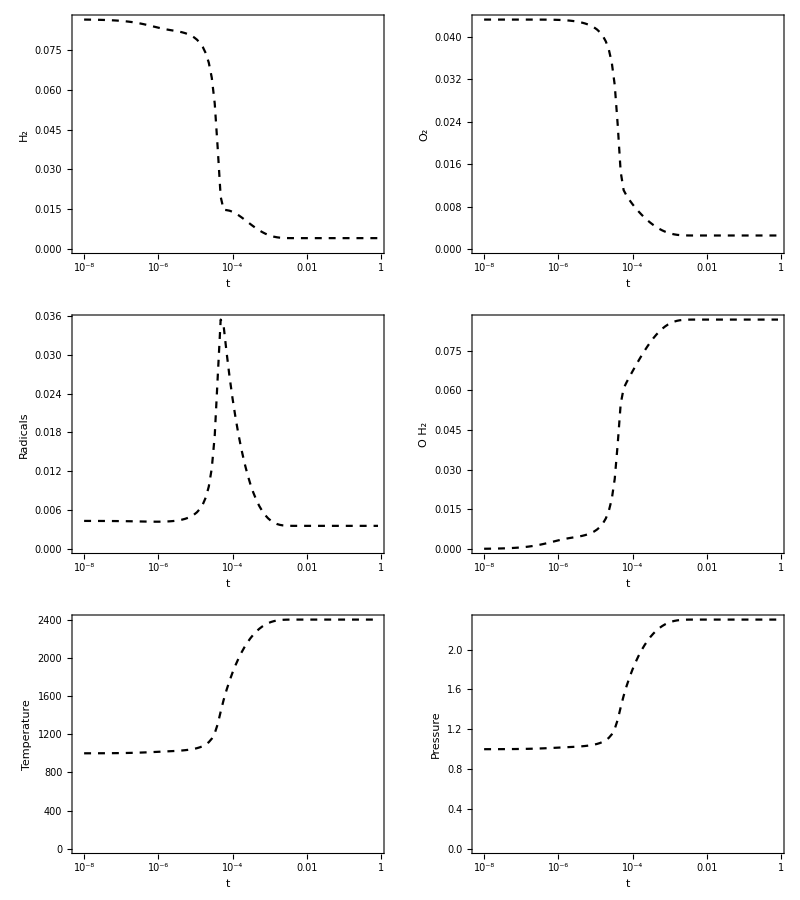

```mathematica
dat=Import["data/h2o2.csv"];
{{p0,p1},{p2,p3},{p4,p5}}={{ListLogLinearPlot[Transpose[{dat[[2;;-1,1]],dat[[2;;-1,4]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[1]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350,PlotStyle->Directive[Black,Dashed]],ListLogLinearPlot[Transpose[{dat[[2;;-1,1]],dat[[2;;-1,7]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[4]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350,PlotStyle->Directive[Black,Dashed]]},{ListLogLinearPlot[Transpose[{dat[[2;;-1,1]],dat[[2;;-1,5]]+dat[[2;;-1,6]]+dat[[2;;-1,8]]+dat[[2;;-1,10]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,HoldForm["Radicals" ]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350,PlotStyle->Directive[Black,Dashed]],ListLogLinearPlot[Transpose[{dat[[2;;-1,1]],dat[[2;;-1,9]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[6]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350,PlotStyle->Directive[Black,Dashed]]},{ListLogLinearPlot[Transpose[{dat[[2;;-1,1]],dat[[2;;-1,2]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,"Temperature"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350,PlotStyle->Directive[Black,Dashed]],ListLogLinearPlot[Transpose[{dat[[2;;-1,1]],dat[[2;;-1,3]]}],PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,"Pressure"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350,PlotStyle->Directive[Black,Dashed]]}};
Grid[{{p0,p1},{p2,p3},{p4,p5}}]
```

## Concentration evolutions

data/h2o2/

{35.4041,Null}

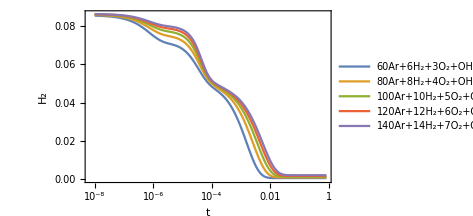
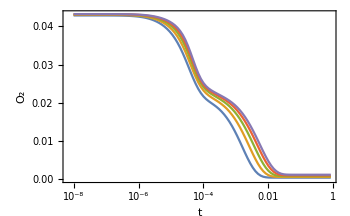
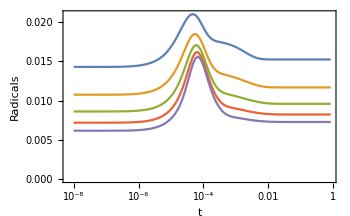
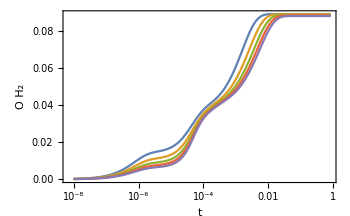
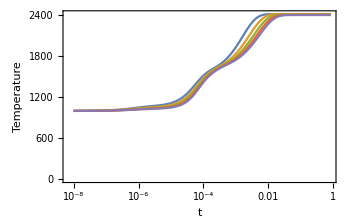
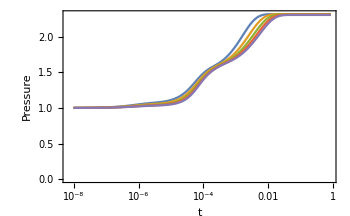

```mathematica
o2dats={};
h2dats={};
h2odats={};
radicaldats={};
temperaturedats={};
pressuredats={};
initials={};
filebase0="data/h2o2/"
AbsoluteTiming[Monitor[Do[filebase=filebase0<>ToString[m]<>"/";
dat=Import[filebase<>"out.dat"];
{atoms, dim,runtime, count, level} = dat[[1,1;;5]];
evals=#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2];
evecs=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],dim];
spatoms=Partition[BinaryReadList[filebase<>"spatoms.npy","Integer64"][[17;;-1]],Length[elements]];
multiindices=Partition[BinaryReadList[filebase<>"multiindices.npy","Integer64"][[17;;-1]],Length[spatoms]];
temperatures=BinaryReadList[filebase<>"temperatures.npy","Real64"][[17;;-1]];
pressures=BinaryReadList[filebase<>"pressures.npy","Real64"][[17;;-1]];
spforms=Table[DisplayForm[RowBox[Table[If[spatoms[[i,j]]>0,If[spatoms[[i,j]]>1,Subscript[elements[[j]],spatoms[[i,j]]],elements[[j]]],""],{j,1,Length[elements]}]]],{i,1,Length[spatoms]}];
ind=1;
initial=Total[DeleteCases[If[#[[1]]>0, If[#[[1]]==1,DisplayForm[RowBox[{ToString[#[[2]]]}]], DisplayForm[RowBox[{#[[1]],#[[2]]}]]]]&/@Transpose[Table[{multiindices[[i]],spforms},{i,1,dim}][[ind]]],Null]];
AppendTo[initials,initial];
states=Partition[BinaryReadList[filebase<>"propogate.npy","Real64"][[17;;-1]],dim];
times=BinaryReadList[filebase<>"times.npy","Real64"][[17;;-1]];
o2norm=DiagonalMatrix[((#[[4]])/Total[#])&/@multiindices];
h2norm=DiagonalMatrix[((#[[1]])/Total[#])&/@multiindices];
h2onorm=DiagonalMatrix[((#[[6]])/Total[#])&/@multiindices];
radicalnorm=DiagonalMatrix[((#[[2]]+#[[3]]+#[[5]]+#[[7]])/Total[#])&/@multiindices];
temperaturenorm=DiagonalMatrix[temperatures];
pressurenorm=DiagonalMatrix[pressures];
(*Abs[(Total[#]-Total[evecs[[-1]].h2norm]/Total[evecs[[-1]]])]*)
AppendTo[h2dats,Transpose[{times,Total[#]&/@(states.h2norm)}]];
AppendTo[o2dats,Transpose[{times,Total[#]&/@(states.o2norm)}]];
AppendTo[radicaldats,Transpose[{times,Total[#]&/@(states.radicalnorm)}]];
AppendTo[h2odats,Transpose[{times,Total[#]&/@(states.h2onorm)}]];
AppendTo[temperaturedats,Transpose[{times,Total[#]&/@(states.temperaturenorm)}]];
AppendTo[pressuredats,Transpose[{times,Total[#]&/@(states.pressurenorm)}]];
p=Legended[ListLogLinearPlot[radicaldats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,HoldForm["Radicals" ]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],Placed[LineLegend[ColorData[97,"ColorList"],initials],Right]];,{m,3,7}],{m,n, p}]]
p=Legended[{{ListLogLinearPlot[h2dats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[1]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],ListLogLinearPlot[o2dats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[4]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350]},{ListLogLinearPlot[radicaldats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,HoldForm["Radicals" ]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],ListLogLinearPlot[h2odats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,spforms[[6]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350]},{ListLogLinearPlot[temperaturedats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,"Temperature"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],ListLogLinearPlot[pressuredats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,"Pressure"},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350]}},Placed[LineLegend[ColorData[97,"ColorList"],initials],Right]]
```

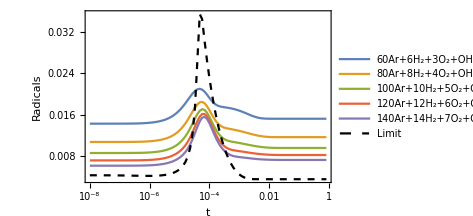

```mathematica
Legended[Show[ListLogLinearPlot[radicaldats,PlotRange->All,Joined->True,Axes->False,Frame->True,FrameLabel->{t,HoldForm["Radicals" ]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],ImageSize->350],p2,PlotRange->All],Placed[LineLegend[Join[ColorData[97,"ColorList"][[1;;Length[initials]]],{Directive[Black,Dashed]}],Join[initials,{"Limit"}]],Right]]
```